```mathematica
t1a=4;t1r=.4; cc=horse8;
```

```mathematica
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];isoTable=startIsoTable[pt,cc];
kthIter=1;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest2[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
```

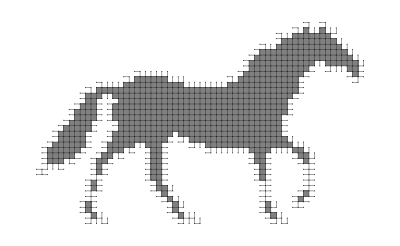

```mathematica
showCC2D[restoreAfterEThinning2[kft,cc]]
```

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
```

```mathematica
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
```

```mathematica
spNum
```

415

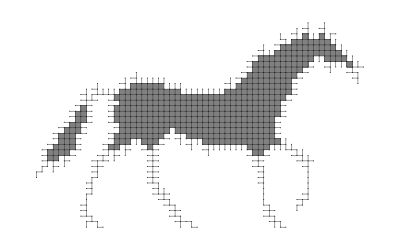

```mathematica
showCC2D[restoreAfterEThinning2[kft,cc]]
```